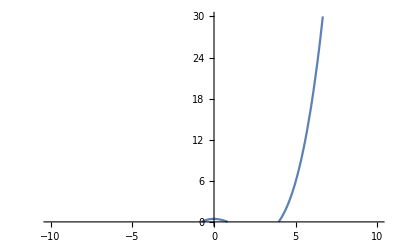

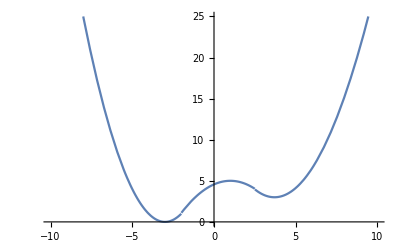

```mathematica
f[x_]:=If[x<-2, (x+3)^2,0]+If[x>=-2&&x<2.5,-(x-1)^2/2.3+5,0]+If[x>=2.5,(x-3.7)^2/1.5+3,0];
Plot[f[x], {x, -10, 10}, PlotRange->{{-10, 10}, {0, 25}}]
```

```mathematica
xdata = Table[f[i], {i, -10, 10, 1}]
```

{49,36,25,16,9,4,1,0,1.08696,3.26087,4.56522,5.,4.56522,3.32667,3.06,4.12667,6.52667,10.26,15.3267,21.7267,29.46}

```mathematica
ydata = Subdivide[-11, 11, 20]
```

{-11,-99/10,-44/5,-77/10,-33/5,-11/2,-22/5,-33/10,-11/5,-11/10,0,11/10,11/5,33/10,22/5,11/2,33/5,77/10,44/5,99/10,11}

```mathematica
Transpose[{xdata, ydata}]
```

{{49,-11},{36,-99/10},{25,-44/5},{16,-77/10},{9,-33/5},{4,-11/2},{1,-22/5},{0,-33/10},{1.08696,-11/5},{3.26087,-11/10},{4.56522,0},{5.,11/10},{4.56522,11/5},{3.32667,33/10},{3.06,22/5},{4.12667,11/2},{6.52667,33/5},{10.26,77/10},{15.3267,44/5},{21.7267,99/10},{29.46,11}}

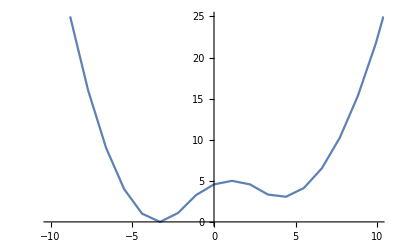

```mathematica
ListLinePlot[Transpose[{ydata, xdata}],PlotRange->{{-10, 10}, {0, 25}}]
```

```mathematica
fit = FindFit[Transpose[{ydata, xdata}], a+b*x+c*x^2+d*x^3+e*x^4+g*x^5+h*x^6+k*x^7+l*x^8+m*x^9, {a, b, c, d, e,g,h,k,l,m}, x]
```

{a→4.35346,b→0.939579,c→-0.356245,d→-0.0465983,e→0.014598,g→0.000676189,h→-0.00012645,k→-5.42826×10^-6,l→4.12025×10^-7,m→1.64564×10^-8}

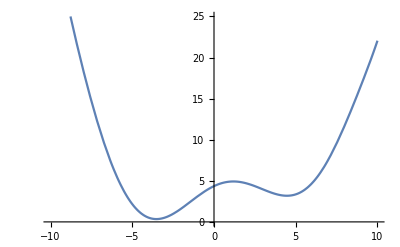

```mathematica
Plot[a+b*x+c*x^2+d*x^3+e*x^4+g*x^5+h*x^6+k*x^7+l*x^8+m*x^9/.fit, {x, -10, 10},PlotRange->{{-10, 10}, {0, 25}}]
```